```mathematica
Clear["Global`*"]
```

```mathematica
t = 100;
n=100;
γ = 1./(2. Sqrt[2.]);
H = Table[
	If[i == j, 2*γ ,
		If[ i == j+1|| i == j-1, -γ, 0]
	],
	{i, 2 n +1},
	{j, 2 n +1}	
 ];
```

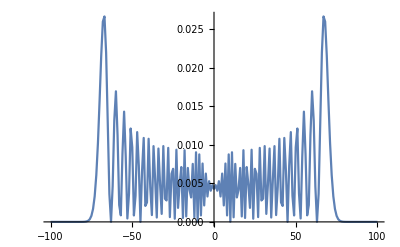

```mathematica
expH = MatrixExp[-I H t];
Psi = expH.Table[If[i == n+1, 1,0],{i, 2*n+1}];
ListLinePlot[Table[{i-1-n, Abs[Psi[[i]]]^2},{i, 2*n+1}]]
```

```mathematica
Length[Psi]
```

201

```mathematica
position = {}
```

{}

```mathematica
For[i=-100, i≤100, i++ , AppendTo[position,i]]
```

```mathematica
probability=Table[{i-1-n, Abs[Psi[[i]]]^2},{i, 2*n+1}]
```

{{-100,2.20751×10^-18},{-99,9.04967×10^-18},{-98,5.49274×10^-17},{-97,3.01006×10^-16},{-96,1.62087×10^-15},{-95,8.45309×10^-15},{-94,4.27644×10^-14},{-93,2.09642×10^-13},{-92,9.95198×10^-13},{-91,4.57117×10^-12},{-90,2.02988×10^-11},{-89,8.70653×10^-11},{-88,3.60362×10^-10},{-87,1.43782×10^-9},{-86,5.52411×10^-9},{-85,2.04123×10^-8},{-84,7.24482×10^-8},{-83,2.46636×10^-7},{-82,8.04092×10^-7},{-81,2.50629×10^-6},{-80,7.4544×10^-6},{-79,0.000021112},{-78,0.0000567998},{-77,0.000144773},{-76,0.000348502},{-75,0.000789445},{-74,0.00167565},{-73,0.00331553},{-72,0.006077},{-71,0.0102359},{-70,0.0156795},{-69,0.0215343},{-68,0.025977},{-67,0.0266488},{-66,0.0219579},{-65,0.0128542},{-64,0.00363097},{-63,0.0000184764},{-62,0.00461271},{-61,0.0131796},{-60,0.0169407},{-59,0.011253},{-58,0.00219655},{-57,0.000852343},{-56,0.00882387},{-55,0.0143021},{-54,0.00848331},{-53,0.000444585},{-52,0.00365986},{-51,0.0121138},{-50,0.0096567},{-49,0.000835784},{-48,0.00338741},{-47,0.0116482},{-46,0.00727135},{-45,9.11366×10^-6},{-44,0.00663081},{-43,0.0108908},{-42,0.0020697},{-41,0.00253158},{-40,0.0107831},{-39,0.00451165},{-38,0.000884993},{-37,0.00982932},{-36,0.00547689},{-35,0.000565845},{-34,0.00951687},{-33,0.00490381},{-32,0.00103635},{-31,0.00983358},{-30,0.00299824},{-29,0.00277752},{-28,0.00960104},{-27,0.000619903},{-26,0.00623642},{-25,0.00688443},{-24,0.000412116},{-23,0.00936114},{-22,0.00181824},{-21,0.00493078},{-20,0.00711478},{-19,0.00050645},{-18,0.00930126},{-17,0.000707365},{-16,0.0069981},{-15,0.00415433},{-14,0.00317071},{-13,0.0075258},{-12,0.000595897},{-11,0.00903198},{-10,0.0000265997},{-9,0.00875684},{-8,0.000839757},{-7,0.00757264},{-6,0.00213516},{-5,0.00626934},{-4,0.00329538},{-3,0.00528303},{-2,0.00404152},{-1,0.00477319},{0,0.00429379},{1,0.00477319},{2,0.00404152},{3,0.00528303},{4,0.00329538},{5,0.00626934},{6,0.00213516},{7,0.00757264},{8,0.000839757},{9,0.00875684},{10,0.0000265997},{11,0.00903198},{12,0.000595897},{13,0.0075258},{14,0.00317071},{15,0.00415433},{16,0.0069981},{17,0.000707365},{18,0.00930126},{19,0.00050645},{20,0.00711478},{21,0.00493078},{22,0.00181824},{23,0.00936114},{24,0.000412116},{25,0.00688443},{26,0.00623642},{27,0.000619903},{28,0.00960104},{29,0.00277752},{30,0.00299824},{31,0.00983358},{32,0.00103635},{33,0.00490381},{34,0.00951687},{35,0.000565845},{36,0.00547689},{37,0.00982932},{38,0.000884993},{39,0.00451165},{40,0.0107831},{41,0.00253158},{42,0.0020697},{43,0.0108908},{44,0.00663081},{45,9.11366×10^-6},{46,0.00727135},{47,0.0116482},{48,0.00338741},{49,0.000835784},{50,0.0096567},{51,0.0121138},{52,0.00365986},{53,0.000444585},{54,0.00848331},{55,0.0143021},{56,0.00882387},{57,0.000852343},{58,0.00219655},{59,0.011253},{60,0.0169407},{61,0.0131796},{62,0.00461271},{63,0.0000184764},{64,0.00363097},{65,0.0128542},{66,0.0219579},{67,0.0266488},{68,0.025977},{69,0.0215343},{70,0.0156795},{71,0.0102359},{72,0.006077},{73,0.00331553},{74,0.00167565},{75,0.000789445},{76,0.000348502},{77,0.000144773},{78,0.0000567998},{79,0.000021112},{80,7.4544×10^-6},{81,2.50629×10^-6},{82,8.04092×10^-7},{83,2.46636×10^-7},{84,7.24482×10^-8},{85,2.04123×10^-8},{86,5.52411×10^-9},{87,1.43782×10^-9},{88,3.60362×10^-10},{89,8.70653×10^-11},{90,2.02988×10^-11},{91,4.57117×10^-12},{92,9.95198×10^-13},{93,2.09642×10^-13},{94,4.27644×10^-14},{95,8.45309×10^-15},{96,1.62087×10^-15},{97,3.01006×10^-16},{98,5.49274×10^-17},{99,9.04967×10^-18},{100,2.20751×10^-18}}

```mathematica
nmean=0;
nmean2=0;
```

```mathematica
For[i=1, i≤201, i++ , 
	nmean2 =nmean2  +(position[[i]]^2)*Abs[Psi[[i]]]^2;
	nmean =nmean+ position[[i]]*Abs[Psi[[i]]]^2
	]
```

```mathematica
Sqrt[nmean2-nmean]
```

50.

```mathematica
FullSimplify[Integrate[Exp[-I (kp-k)x],{kp,-Pi,Pi}]/(2Pi)]
```

(Sin[3.14159 x] (0.31831 Cos[k x]+(0.+0.31831 ⅈ) Sin[k x]))/x

```mathematica
InverseFourierTransform[Exp[I k x],k,x]
```

InverseFourierTransform[ⅇ^(ⅈ k x),k,x]

```mathematica
Htilt = 1/(√2){{Exp[-I k],Exp[-I k]},{Exp[I k],-Exp[I k]}}
```

{{ⅇ^(-ⅈ k)/(√2),ⅇ^(-ⅈ k)/(√2)},{ⅇ^(ⅈ k)/(√2),-ⅇ^(ⅈ k)/(√2)}}

```mathematica
Eigenvectors[Htilt]
```

{{-1/2 ⅇ^(-2 ⅈ k) (-1-ⅇ^(2 ⅈ k)+√(1+6 ⅇ^(2 ⅈ k)+ⅇ^(4 ⅈ k))),1},{1/2 ⅇ^(-2 ⅈ k) (1+ⅇ^(2 ⅈ k)+√(1+6 ⅇ^(2 ⅈ k)+ⅇ^(4 ⅈ k))),1}}

```mathematica
α = {-1/2 ⅇ^(-2 ⅈ k) (-1-ⅇ^(2 ⅈ k)+√(1+6 ⅇ^(2 ⅈ k)+ⅇ^(4 ⅈ k))),1};
β = {1/2 ⅇ^(-2 ⅈ k) (1+ⅇ^(2 ⅈ k)+√(1+6 ⅇ^(2 ⅈ k)+ⅇ^(4 ⅈ k))),1};
```

```mathematica
FullSimplify[Normalize[α],Assumptions->k ∈ Reals]
```

{(ⅇ^(-2 ⅈ k) (1+ⅇ^(2 ⅈ k)-√(1+6 ⅇ^(2 ⅈ k)+ⅇ^(4 ⅈ k))))/(√(4+Abs[1+ⅇ^(2 ⅈ k)-√(1+6 ⅇ^(2 ⅈ k)+ⅇ^(4 ⅈ k))]^2)),2/(√(4+Abs[1+ⅇ^(2 ⅈ k)-√(1+6 ⅇ^(2 ⅈ k)+ⅇ^(4 ⅈ k))]^2))}

```mathematica
FullSimplify[Normalize[β],Assumptions->k ∈ Reals]
```

{(ⅇ^(-2 ⅈ k) (1+ⅇ^(2 ⅈ k)+√(1+6 ⅇ^(2 ⅈ k)+ⅇ^(4 ⅈ k))))/(√(4+Abs[1+ⅇ^(2 ⅈ k)+√(1+6 ⅇ^(2 ⅈ k)+ⅇ^(4 ⅈ k))]^2)),2/(√(4+Abs[1+ⅇ^(2 ⅈ k)+√(1+6 ⅇ^(2 ⅈ k)+ⅇ^(4 ⅈ k))]^2))}

```mathematica
Eigenvalues[Htilt]
```

{(ⅇ^(-ⅈ k) (1-ⅇ^(2 ⅈ k)-√(1+6 ⅇ^(2 ⅈ k)+ⅇ^(4 ⅈ k))))/(2 √2),(ⅇ^(-ⅈ k) (1-ⅇ^(2 ⅈ k)+√(1+6 ⅇ^(2 ⅈ k)+ⅇ^(4 ⅈ k))))/(2 √2)}